```mathematica
Quit[]
```

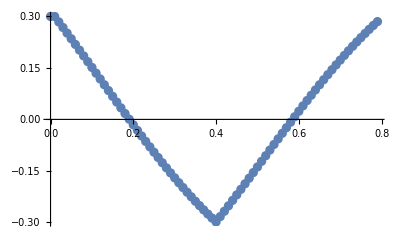

{A→-0.252084,ω→-7.87212,ϕ→4.64412}

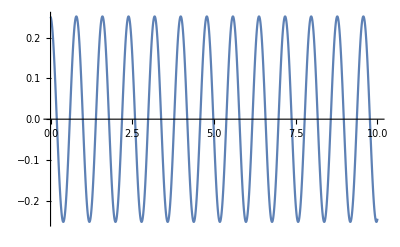

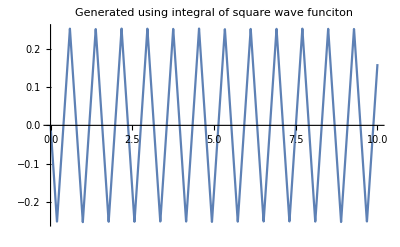

```mathematica
q = Flatten[Import["C:\\Users\\Mahdieh\\OneDrive\\Documents\\MSR Spring Quarter 2015\\CPG\\project\\CPG_project-990d01ecd314bdd3870e1b46760f62271f1f77e0\\CPG_project-990d01ecd314bdd3870e1b46760f62271f1f77e0\\x_ref.csv"]][[1;;80]];
time = Table[i*0.01,{i,0,Length[q]-1}];
data = Thread[{time,q}];
scatter =ListPlot[data]
sol = FindFit[data,A*Sin[ω*t+ϕ] (*+B*Sin[ω2*t+ϕ2]*),{A,ω,ϕ},t,MaxIterations->1000,AccuracyGoal->6,PrecisionGoal->6]
approx[t_]:= A*Sin[ω*t+ϕ] (*+B*Sin[ω2*t+ϕ2]*);
triangle = TriangleWave[{-0.252, 0.252},x];
tri = 2* 0.252/Pi ArcSin[Sin[2 Pi x/ -.79]]; 
Plot[approx[t]/.sol,{t,0,10}]
(*Plot[triangle, {x, 0, 10}, PlotLabel-> " Built-in TrianlgeWave function "]*)
Plot[tri, {x, 0, 10}, PlotLabel-> " Generated using integral of square wave funciton"]
```